```mathematica
(*Initialize value*)
```

```mathematica
BoundaryVertices={{-0.5952140056526223,0.23287047608171996},{-0.4954917379727142,0.8562602048203958},{-0.3290035917040952,0.8141768599435786},{-0.02928041096296896,0.5539553994693478},{-0.005663507996275019,0.3197655120590299},{0.,0.}};
AreaWeight={0.0298168,0.042471,0.0440136,0.0102628,0.0394658,0.0445043,0.0408803,0.0307868,0.0262848,0.0318225};
```

```mathematica
InitialGeneratorPosition={{-0.28765825222989466,0.418681632979253},{-0.433123557367,0.553111495308},{-0.4,0.6},{-0.488745117961,0.416008279297},{-0.452376160754,0.171571056169},{-0.264580915194,0.402574218711},{-0.253336968199,0.233201740456},{-0.4,0.2},{-0.00584316866592,0.0843194842314},{-0.2,0.2}};
```

```mathematica
(*Compute Distance between Generators and specify topo *)
RadiiSet={};
For[i=1,i≤Length[InitialGeneratorPosition],i++,
SetDiff=Complement[InitialGeneratorPosition,{InitialGeneratorPosition[[i]]}];
RadiiSet1={};
For[j=1,j≤Length[SetDiff],j++,
RadiiSet1=Join[RadiiSet1,{EuclideanDistance[InitialGeneratorPosition[[i]],SetDiff[[j]]]}];
];
MinRad=Min[RadiiSet1];
RadiiSet=Join[RadiiSet,{MinRad}]
];
RadiiForTopo=RadiiSet/2;
(*Construction of Topological Circles *)
CircleSet={};
For[i=1,i≤Length[InitialGeneratorPosition],i++,
CircleSet=Join[CircleSet,{Region[Disk[InitialGeneratorPosition[[i]],RadiiForTopo[[i]]]]}];
]
```

```mathematica
(*Define Function D(V(S),C)*)
```

```mathematica
CCVTFunction[CoordinateOpt_]:=Block[{i,j,k},
Distance=0;
m=VoronoiMesh[CoordinateOpt,{{-4,4},{-5,5}}];
p=BoundaryVertices//Polygon//DiscretizeGraphics;

A=DeleteCases[RegionIntersection[DiscretizeGraphics@#,p]&/@MeshPrimitives[m,2],_RegionIntersection]//RegionPlot[#,AspectRatio->Automatic]&;
Mm=DeleteCases[RegionIntersection[DiscretizeGraphics@#,p]&/@MeshPrimitives[m,2],_RegionIntersection];
(*Print[Show[A,ListPlot[Table[Labeled[CoordinateOpt[[i]],i],{i,Length[CoordinateOpt]}]]]];*)

(*Sort the MeshPrimitives: Compute the distance btw polygons and point. The smallest distance will be the order of Voronoi mesh*)
If[Length[CoordinateOpt]=!=Length[Mm],FunctionResult=100000000,
PolySet={};
For[i=1,i≤Length[CoordinateOpt],i++,
DistanceBTWPoly={};
For[j=1,j≤Length[CoordinateOpt],j++,
DistanceBTWPoly=Join[DistanceBTWPoly,{RegionDistance[Mm[[j]],CoordinateOpt[[i]]]}];
];
PolySet=Join[PolySet,{Position[DistanceBTWPoly,Min[DistanceBTWPoly]][[1]][[1]]}];
];
(*Sort the VD Region *)
SortVDCell={};
For[k=1,k≤Length[PolySet],k++,
SortVDCell=Join[SortVDCell,{Mm[[PolySet[[k]]]]}]
];
(*Compute Area of each cell*)
ComputedArea={};
For[i=1,i≤Length[SortVDCell],i++,
ComputedArea=Join[ComputedArea,{Area[SortVDCell[[i]]]}]
];
(*Compute perimeter ratio for compactness *)
AreaCircle={};
For[i=1,i≤Length[SortVDCell],i++,
AreaCirc=(Perimeter[Mm[[i]]])^2/(4Pi);
AreaCircle=Join[AreaCircle,{Area[SortVDCell[[i]]]/AreaCirc}]
];
(*Compute the average area of each cell*)
Avg=Area[Polygon[BoundaryVertices]]/Length[InitialGeneratorPosition];
PernaltyCompactness=Avg*(Length[InitialGeneratorPosition]-Total[AreaCircle])^2;
(*Sum of the distance*)
For[k=1,k≤Length[ComputedArea],k++,
Distance=Distance+(AreaWeight[[k]]-(ComputedArea[[k]]))^2
];
(*Condition of Pernalty*)
Pernalty=0;
For[i=1,i≤Length[CoordinateOpt],i++,
If[RegionDistance[Polygon[BoundaryVertices],CoordinateOpt[[i]]]>0,
(*Add pernalty*)
Pernalty=Pernalty+(RegionDistance[Polygon[BoundaryVertices],CoordinateOpt[[i]]]*AreaWeight[[i]])^2;
]
];
(*Pernalty for Topological Structure*)
PernaltyTopo=0;
For[i=1,i≤Length[CoordinateOpt],i++,
If[ RegionMember[CircleSet[[i]],CoordinateOpt[[i]]],,
PernaltyTopo=PernaltyTopo+100*(RegionDistance[CircleSet[[i]],CoordinateOpt[[i]]]*AreaWeight[[i]])^2;
]
];
FunctionResult=Distance+Pernalty+PernaltyCompactness+PernaltyTopo
(*Print[" FunctionResult =",FunctionResult];
Print[" Penalty =",Pernalty];
Print[" PenaltyCompactness =", PernaltyCompactness];
Print[" PernaltyTopo =", PernaltyTopo];*)
]
]
```

```mathematica
CCVTFunction[InitialGeneratorPosition]
```

0.241493

```mathematica
CCVTFunctionPlot[CoordinateOpt_]:=Block[{i,j,k},
Distance=0;
m=VoronoiMesh[CoordinateOpt,{{-4,4},{-5,5}}];
p=BoundaryVertices//Polygon//DiscretizeGraphics;


A=DeleteCases[RegionIntersection[DiscretizeGraphics@#,p]&/@MeshPrimitives[m,2],_RegionIntersection]//RegionPlot[#,AspectRatio->Automatic]&;
Mm=DeleteCases[RegionIntersection[DiscretizeGraphics@#,p]&/@MeshPrimitives[m,2],_RegionIntersection];
Print[Show[A,ListPlot[Table[Labeled[CoordinateOpt[[i]],i],{i,Length[CoordinateOpt]}]]]];

(*Sort the MeshPrimitives: Compute the distance btw polygons and point. The smallest distance will be the order of Voronoi mesh*)
If[Length[CoordinateOpt]=!=Length[Mm],FunctionResult=100000000,
PolySet={};
For[i=1,i≤Length[CoordinateOpt],i++,
DistanceBTWPoly={};
For[j=1,j≤Length[CoordinateOpt],j++,
DistanceBTWPoly=Join[DistanceBTWPoly,{RegionDistance[Mm[[j]],CoordinateOpt[[i]]]}];
];
PolySet=Join[PolySet,{Position[DistanceBTWPoly,Min[DistanceBTWPoly]][[1]][[1]]}];
];
(*Sort the VD Region *)
SortVDCell={};
For[k=1,k≤Length[PolySet],k++,
SortVDCell=Join[SortVDCell,{Mm[[PolySet[[k]]]]}]
];
(*Compute Area of each cell*)
ComputedArea={};
For[i=1,i≤Length[SortVDCell],i++,
ComputedArea=Join[ComputedArea,{Area[SortVDCell[[i]]]}]
];
(*Compute perimeter ratio for compactness *)
AreaCircle={};
For[i=1,i≤Length[SortVDCell],i++,
AreaCirc=(Perimeter[Mm[[i]]])^2/(4Pi);
AreaCircle=Join[AreaCircle,{Area[SortVDCell[[i]]]/AreaCirc}]
];
(*Compute the average area of each cell*)
Avg=Area[Polygon[BoundaryVertices]]/Length[InitialGeneratorPosition];
PernaltyCompactness=Avg*(Length[InitialGeneratorPosition]-Total[AreaCircle])^2;
(*Sum of the distance*)
For[k=1,k≤Length[ComputedArea],k++,
Distance=Distance+(AreaWeight[[k]]-(ComputedArea[[k]]))^2
];
(*Condition of Pernalty*)
Pernalty=0;
For[i=1,i≤Length[CoordinateOpt],i++,
If[RegionDistance[Polygon[BoundaryVertices],CoordinateOpt[[i]]]>0,
(*Add pernalty*)
Pernalty=Pernalty+(RegionDistance[Polygon[BoundaryVertices],CoordinateOpt[[i]]]*AreaWeight[[i]])^2;
]
];
PernaltyTopo=0;
For[i=1,i≤Length[CoordinateOpt],i++,
If[ RegionMember[CircleSet[[i]],CoordinateOpt[[i]]],,
PernaltyTopo=PernaltyTopo+100*(RegionDistance[CircleSet[[i]],CoordinateOpt[[i]]]*AreaWeight[[i]])^2;
]
];
FunctionResult=Distance+Pernalty+PernaltyCompactness+PernaltyTopo
]
]
```

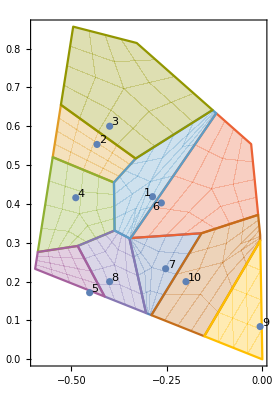

0.241493

```mathematica
CCVTFunctionPlot[InitialGeneratorPosition]
```

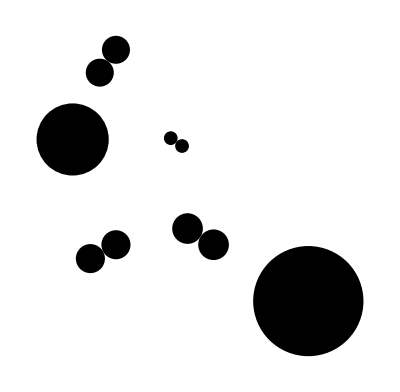

```mathematica
Show[CircleSet]
```

```mathematica
CCVTFunction1[CoordinateOpt_]:=Block[{i,j,k},
Distance=0;
m=VoronoiMesh[CoordinateOpt,{{-4,4},{-5,5}}];
p=BoundaryVertices//Polygon//DiscretizeGraphics;

A=DeleteCases[RegionIntersection[DiscretizeGraphics@#,p]&/@MeshPrimitives[m,2],_RegionIntersection]//RegionPlot[#,AspectRatio->Automatic]&;
Mm=DeleteCases[RegionIntersection[DiscretizeGraphics@#,p]&/@MeshPrimitives[m,2],_RegionIntersection];
(*Print[Show[A,ListPlot[Table[Labeled[CoordinateOpt[[i]],i],{i,Length[CoordinateOpt]}]]]];*)

(*Sort the MeshPrimitives: Compute the distance btw polygons and point. The smallest distance will be the order of Voronoi mesh*)
If[Length[CoordinateOpt]=!=Length[Mm],FunctionResult=100000000,
PolySet={};
For[i=1,i≤Length[CoordinateOpt],i++,
DistanceBTWPoly={};
For[j=1,j≤Length[CoordinateOpt],j++,
DistanceBTWPoly=Join[DistanceBTWPoly,{RegionDistance[Mm[[j]],CoordinateOpt[[i]]]}];
];
PolySet=Join[PolySet,{Position[DistanceBTWPoly,Min[DistanceBTWPoly]][[1]][[1]]}];
];
(*Sort the VD Region *)
SortVDCell={};
For[k=1,k≤Length[PolySet],k++,
SortVDCell=Join[SortVDCell,{Mm[[PolySet[[k]]]]}]
];
(*Compute Area of each cell*)
ComputedArea={};
For[i=1,i≤Length[SortVDCell],i++,
ComputedArea=Join[ComputedArea,{Area[SortVDCell[[i]]]}]
];
(*Compute perimeter ratio for compactness *)
AreaCircle={};
For[i=1,i≤Length[SortVDCell],i++,
AreaCirc=(Perimeter[Mm[[i]]])^2/(4Pi);
AreaCircle=Join[AreaCircle,{Area[SortVDCell[[i]]]/AreaCirc}]
];
(*Compute the average area of each cell*)
Avg=Area[Polygon[BoundaryVertices]]/Length[InitialGeneratorPosition];
PernaltyCompactness=Avg*(Length[InitialGeneratorPosition]-Total[AreaCircle])^2;
(*Sum of the distance*)
For[k=1,k≤Length[ComputedArea],k++,
Distance=Distance+(AreaWeight[[k]]-(ComputedArea[[k]]))^2
];
(*Condition of Pernalty*)
Pernalty=0;
For[i=1,i≤Length[CoordinateOpt],i++,
If[RegionDistance[Polygon[BoundaryVertices],CoordinateOpt[[i]]]>0,
(*Add pernalty*)
Pernalty=Pernalty+(RegionDistance[Polygon[BoundaryVertices],CoordinateOpt[[i]]]*AreaWeight[[i]])^2;
]
];
(*Pernalty for Topological Structure*)
PernaltyTopo=0;
For[i=1,i≤Length[CoordinateOpt],i++,
If[ RegionMember[CircleSet[[i]],CoordinateOpt[[i]]],,
PernaltyTopo=PernaltyTopo+100*(RegionDistance[CircleSet[[i]],CoordinateOpt[[i]]]*AreaWeight[[i]])^2;
]
];
FunctionResult=Distance+Pernalty+PernaltyCompactness+PernaltyTopo;
Print[" FunctionResult =",FunctionResult];
Print[" AreaError =",Distance];
Print[" Penalty =",Pernalty];
Print[" PenaltyCompactness =", PernaltyCompactness];
Print[" PernaltyTopo =", PernaltyTopo];
]
]
```